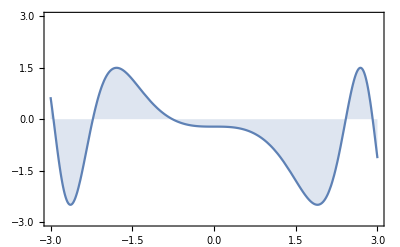

```mathematica
g=Plot[2*Sin[x^3/4+3]-0.5,{x,-3,3},PlotRange->{{-3,3},{-3,3}} ,Filling->Axis,Frame->True];
Show[g,ImageSize->Scaled[0.5]]
```

```mathematica
NIntegrate[2*Sin[x^3/4+3]-0.5,{x,-3,3}]
```

-2.27701

```mathematica
NumberForm[-2.27700868095657,16]
```

-2.27700868095657

```mathematica
Integrate[Sin[x^2+3],x]
```

√(π/2) (Cos[3] FresnelS[√(2/π) x]+FresnelC[√(2/π) x] Sin[3])